```mathematica
Γ=1.;
δmax=100;tmax=10;
ftarget=δmax/2;
ta=tmax/6;tb=tmax;
δfmod=10;
δ0[t_]:=Which[
t<ta,t/ta ftarget,
(t≥ta)&&(t<tb),ftarget+δfmod Exp[-(t-(ta+tb)/2)^2/5]Sin[20(t-ta)/tmax 4]-.2(t-ta)/ta δmax
];
npts=400;
thepicSYNTH=ListDensityPlot[Table[1/(1+((δ-δ0[t])/(Γ/2))^2),{t,0,tmax,tmax/npts},{δ,-δmax,δmax,(2δmax)/npts}],PlotRange->{0,1},ColorFunction->"Rainbow",AspectRatio->.5,Frame->True,FrameLabel->{Style["Frequency",26],Style["Time",26]},FrameTicks->None]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["SynthesizerPic.jpg",thepicSYNTH,ImageSize->{744,376}];
```

```mathematica
Γ=1.;
δmax=100;tmax=10;
ftarget=δmax/2;
ta=tmax/6;tb=tmax;
δfmod=10;
δ0[t_]:=Which[
t<ta,δmax-t/ta(δmax-ftarget),
(t≥ta)&&(t<tb),ftarget
];
δ1[t_]:=Which[
t<ta,fmax-t/ta(fmax-ftarget),
(t≥ta)&&(t<tb),ftarget+δfmod Exp[-(t-(ta+tb)/2)^2/5]Sin[20(t-ta)/tmax 4]-.2(t-ta)/ta δmax
];
npts=400;NN=5;
thepicMULTISynth=ListDensityPlot[Table[Sum[1/(1+((δ-(δmax/1 jj/NN If[t<tmax/2,t/tmax,1/2+.5(t-tmax/2)/tmax]+δmax/50 If[t>tmax/2,Sin[δmax (t-tmax/2)/tmax],0]))/(Γ/2))^2),{jj,-NN,NN}],{t,0,tmax,tmax/npts},{δ,-δmax,δmax,(2δmax)/npts}],PlotRange->{0,1},ColorFunction->"Rainbow",AspectRatio->.5,Frame->True,FrameLabel->{Style["Frequency",26],Style["Time",26]},FrameTicks->None]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["MultiSynthesizerPic.jpg",thepicMULTISynth,ImageSize->{744,376}];
```

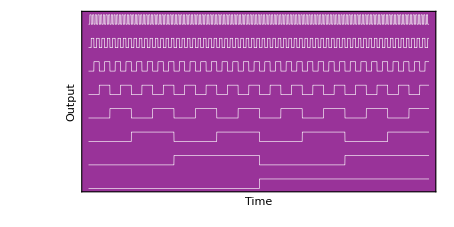

```mathematica
thepicDOG=Plot[Table[j,{j,0,7}]+.4IntegerDigits[Floor[x],2,8],{x,0,255},Frame->True,FrameLabel->{Style["Time",26],Style["Output",26]},FrameTicks->None,PlotStyle->{Thickness[.001],White},AspectRatio->.5,Prolog->{Lighter[Purple,.2],Rectangle[{-10,-.5},{265,8}]}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["DOGPic.jpg",thepicDOG,ImageSize->{744,376}];
```